(1 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -1
0 | 0 | 0 | 0 | 1)

(0
0.046875
0.1875
0.421875
1)

{0.,0.484375,0.921875,1.17187,1.}

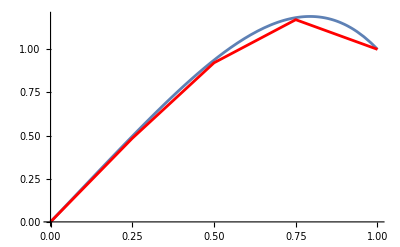

```mathematica
f[x_]:=2*x-Power[x, 4]; (*u0 = 0, u1 = 1*)
n=4;
h = 1.0/n;
F=Table[12*Power[(i*h),2]*h*h,{i,1,n-1}];
K=ConstantArray[0,{n+1,n+1}];
K[[1,1]] = 1;
K[[n+1,n+1]] = 1;
Do[K[[i,i]]=2;
If[i>1 ,K[[i,i-1]]=-1];
If[i<n+1,K[[i,i+1]]=-1];,{i,2,n}];
F = Prepend[F, 0];
F = Append[F, 1];
MatrixForm[K]
MatrixForm[F]
U = LinearSolve[K, F]
xCoords=Table[i*h,{i,0,n}];
normalizedX=Rescale[xCoords];
pairs = Transpose[{normalizedX, U}];
p1= Plot[f[x], {x, 0,1}];
p2 = ListLinePlot[pairs, PlotStyle->Red, PlotRange-> Automatic];
Show[p1, p2]
```